# Versuch 41

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<MaTeX`
```

## Functions

```mathematica
f[{a_,b_}]:=TeXForm@NumberForm[SetAccuracy[a±b,Accuracy@SetPrecision[b,2]],ExponentFunction->(Null&)]//ToString//Quiet
```

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Import Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Stehende Wellen.xlsx"]
```

{{{Frequenz (MHz),peak-peak (mV)},{1.905,22.4},{1.914,21.6},{1.905,22.},{1.908,23.4},{1.905,24.8}},{{Frequenz (kHz),Peak-Peak (mV)},{949.,15.},{938.,14.8},{938.,14.5},{940.,14.5},{940.,15.}},{{Frequenz (MHz),Peak-Peak (mV)},{2.877,26.6},{2.874,27.},{2.876,26.6},{2.879,26.4},{2.881,26.2}}}

```mathematica
meanVal[dat_]:={Mean[dat],StandardDeviation[dat]/Sqrt[Length[dat]]}
```

```mathematica
data=Table[meanVal/@Transpose[rawData[[i,2;;-1]]],{i,1,Length[rawData]}];
```

```mathematica
data
```

{{{1.9074,0.00174929},{22.84,0.574108}},{{941.,2.04939},{14.76,0.11225}},{{2.8774,0.0012083},{26.56,0.132665}}}

```mathematica
f[10^3data[[1,1]]]
f[data[[2,1]]]
f[10^3data[[3,1]]]
```

1907.4\pm 1.7

941.0\pm 2.0

2877.4\pm 1.2

```mathematica
f[data[[1,2]]]
f[data[[2,2]]]
f[data[[3,2]]]
```

22.84\pm 0.57

14.76\pm 0.11

26.56\pm 0.13

```mathematica
{v1, dv1}={10^6 data[[1,1,1]]*(50*2),10^6 data[[1,1,2]]*(50*2)};
{v2, dv2}={10^3 data[[2,1,1]]*(50*4),10^3 data[[2,1,2]]*(50*4)};
{v3, dv3}={10^6 data[[3,1,1]]*(50*4/3),10^6 data[[3,1,2]]*(50*4/3)};
```

```mathematica
f[{v1, dv1}10^(-6)]
f[{v2, dv2}10^(-6)]
f[{v3, dv3}10^(-6)]
```

190.74\pm 0.17

188.20\pm 0.41

191.827\pm 0.081

```mathematica
c=299792458
```

299792458

ϵ = (c/v)^2

dϵ = 2c^2/v^3 dv

```mathematica
{ϵ1, dϵ1}={(c/v1)^2, 2c^2/v1^3 dv1}
{ϵ2, dϵ2}={(c/v2)^2, 2c^2/v2^3 dv2}
{ϵ3, dϵ3}={(c/v3)^2, 2c^2/v3^3 dv3}
```

{2.47035,0.00453113}

{2.53748,0.0110527}

{2.44244,0.0020513}

```mathematica
f[{ϵ1, dϵ1}]
f[{ϵ2, dϵ2}]
f[{ϵ3, dϵ3}]
```

2.4703\pm 0.0045

2.537\pm 0.011

2.4424\pm 0.0021

## Logarithmic Scale

D = 20 log_10 (U0/(U0-Umin))
dD = 20/ln(10) (U0-Umin)/U0 1/U0 dUmin

```mathematica
U0=200;
```

```mathematica
{D1, dD1}={20 Log[10,U0/(U0-data⟦1,2,1⟧)], 20/Log[10](U0-data⟦1,2,1⟧)/U0^2 data[[1,2,2]]}
{D2, dD2}={20 Log[10,U0/(U0-data⟦2,2,1⟧)], 20/Log[10](U0-data⟦2,2,1⟧)/U0^2 data[[2,2,2]]}
{D3, dD3}={20 Log[10,U0/(U0-data⟦3,2,1⟧)], 20/Log[10](U0-data⟦3,2,1⟧)/U0^2 data[[3,2,2]]}
```

{1.05329,0.0220858}

{0.665904,0.00451517}

{1.23761,0.00499643}

```mathematica
f[{D1, dD1}]
f[{D2, dD2}]
f[{D3, dD3}]
```

1.053\pm 0.022

0.6659\pm 0.0045

1.2376\pm 0.0050

```mathematica
frequencies={Around[10^3data[[1,1,1]], 10^3 data[[1,1,2]]],Around[data[[2,1,1]], data[[2,1,2]]], Around[10^3data[[3,1,1]], 10^3 data[[3,1,2]]]}
```

{1907.41.7,941.02.0,2877.41.2}

```mathematica
amplitudes={Around[D1, dD1], Around[D2, dD2], Around[D3, dD3]}
```

{1.0530.022,0.6660.005,1.2380.005}

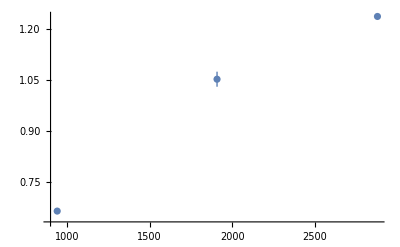

```mathematica
ListPlot[Transpose[{frequencies[[All,1]], {amplitudes[[1]],amplitudes[[2,1]],amplitudes[[3,1]]}}],PlotRange->All]
```

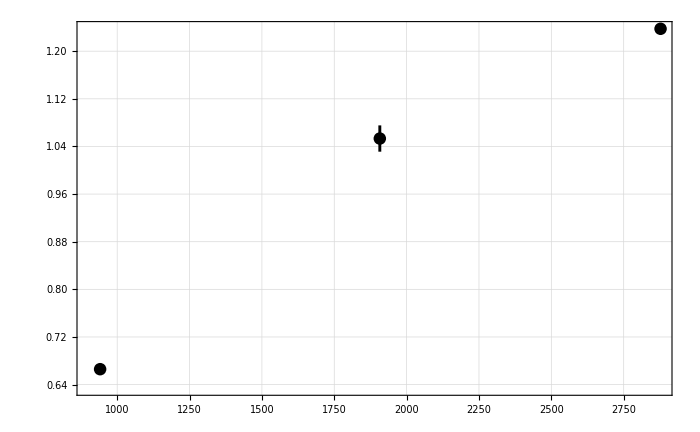

```mathematica
ListPlot[Transpose[{frequencies[[All,1]], {amplitudes[[1]],amplitudes[[2,1]],amplitudes[[3,1]]}}],PlotRange->All,pltsettings,PlotStyle->Directive[Black,Thickness[0.003]],FrameLabel->{MaTeX["\\nu\\text{ [kHz]}",Magnification->2.5], MaTeX["D\\text{ [dB]}",Magnification->2.5]}]
```

```mathematica
Export[NotebookDirectory[]<>"stehende Wellen.pdf",ListPlot[Transpose[{frequencies[[All,1]], {amplitudes[[1]],amplitudes[[2,1]],amplitudes[[3,1]]}}],PlotRange->All,pltsettings,PlotStyle->Directive[Black,Thickness[0.003]],FrameLabel->{MaTeX["\\nu\\text{ [kHz]}",Magnification->2.5], MaTeX["D\\text{ [dB]}",Magnification->2.5]}],Background->None];
```